```mathematica
Interactions 2.1 - Nathan Yee
```

```mathematica
i2={1,0};
j2={0,1};
i3={1,0,0};
j3={0,1,0};
k3={0,0,1};
```

```mathematica
Center of Mass - Calculations
```

```mathematica
Question 3a
```

3 Question

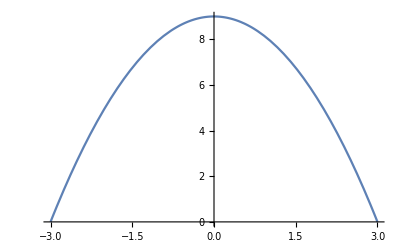

```mathematica
Plot[9-x^2,{x,-3,3}]
```

```mathematica
numer3a=Integrate[(x*i2+y*j2)y,{x,-3,3},{y,0,9-x^2}];
denom3a=Integrate[y,{x,-3,3},{y,0,9-x^2}];
com3a=N[numer3a/denom3a]
```

{0.,5.14286}

```mathematica
Question 3b
```

```mathematica
numer3b=Integrate[(x*i3+y*j3+z*k3)*y,{x,0,1},{y,0,1-x},{z,0,1-x-y}];
denom3b=Integrate[y,{x,0,1},{y,0,1-x},{z,0,1-x-y}];
com3b=numer3b/denom3b
```

{1/5,2/5,1/5}

```mathematica
Question 4
```

```mathematica
numer4a=Integrate[x*i3+y*j3+z*k3,{x,-1/2,1/2},{y,-1/2,1/2},{z,-1/2,1/2}]
denom4a=Integrate[1,{x,-1/2,1/2},{y,-1/2,1/2},{z,-1/2,1/2}]
com4a=numer4a/denom4a
```

{0,0,0}

1

{0,0,0}

```mathematica
numer4b=Integrate[x*i3+y*j3+z*k3,{x,1.5,2.5},{y,-Sqrt[-(x-2)^2+1/4],Sqrt[-(x-2)^2+1/4]},{z,-1/2,1/2}]
denom4b=Integrate[1,{x,1.5,2.5},{y,-Sqrt[-(x-2)^2+1/4],Sqrt[-(x-2)^2+1/4]},{z,-1/2,1/2}]
com4b=numer4b/denom4b
```

{1.5708,0,0}

0.785398

{2.,0.,0.}

```mathematica
Solve[d==.7853(2-d),d]
```

{{d→0.87974}}

```mathematica
Distributed Forces - Computational
```

```mathematica
Question 4
```

```mathematica
numerator4=Integrate[(x*i2+y*j2),{x,0,Sqrt[17]},{y,0,200*Sqrt[1-(x^2/17)]}];
denominator4=N[Integrate[1,{x,0,Sqrt[17]},{y,0,200*Sqrt[1-(x^2/17)]}]]
col4=numerator4/denominator4
```

647.656

{1.7499,84.8826}

```mathematica
Question 5
```

```mathematica
densityAluminum=2.65;
length=2;
thickness=.01
diameter=.15
```

0.01

0.15

```mathematica
bigCylinder=densityAluminum*length*(Pi*(diameter/2)^2)
```

0.0936587

```mathematica
smallCylinder=densityAluminum*(length-2*thickness)*Pi*((diameter-2*thickness)/2)^2
```

0.0696446

```mathematica
weightCylinder=(bigCylinder-smallCylinder)*10^3
```

24.0141

```mathematica
weightCylinder*3
```

72.0423

```mathematica
bigCylinder*3
```

0.280976

```mathematica
weightCylinder/bigCylinder
```

256.4

```mathematica
Clear[x]
```

```mathematica
mass=Solve[1000==(weightCylinder+x)/(bigCylinder),x]
```

{{x→69.6446}}

```mathematica
(69.64463236055437-weightCylinder)
```

45.6305